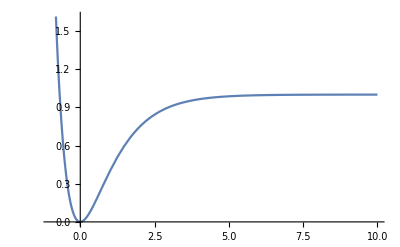

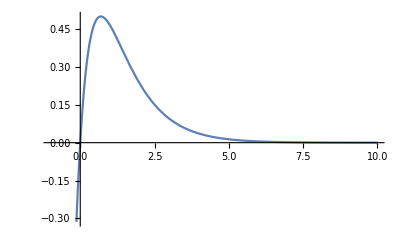

DD α^2 (x-r0)^2-DD α^3 (x-r0)^3+O[x-r0]^4

```mathematica
Clear["`*"]
α=1;r0=0;DD=1;
f[r_]:=DD(1-Exp[-α(r-r0)])^2
Plot[f[x],{x,-1,10}]
Plot[f'[x],{x,-1,10}]
Clear[α,r0,DD]
Series[f[x],{x,r0,3}]
```

```mathematica
f'[x]//Simplify
f'[Log[2]/α+r0]
```

-2 DD ⅇ^((r0-x) α) (-1+ⅇ^((r0-x) α)) α

(DD α)/2

```mathematica
f'[x]//Simplify
```

-2 DD ⅇ^((r0-x) α) (-1+ⅇ^((r0-x) α)) α

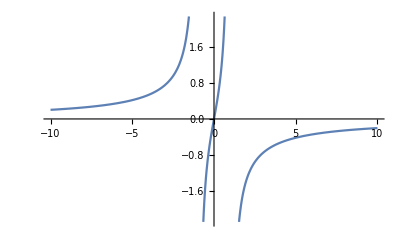

```mathematica
g[x_]:=Log[1/(1-x^2)];
Plot[g'[x],{x,-10,10}]
```

```mathematica
Sqrt[4.5^2+2*2.25]
```

4.97494

```mathematica
ArcTan[3/8*8/3]/Degree//N
```

45.

```mathematica
Tan[π/6]//N
```

0.57735

```mathematica
t={10.6197,20.556,29.3578,43.1524,45}/180*π;
m={2,1,2,2,3};
dy=24;
dy*m*Sin[t]/2//N
dy*m*Cos[t]/2//N
```

{4.42294,4.21347,11.7663,16.4146,25.4558}

{23.5889,11.236,20.9178,17.5089,25.4558}

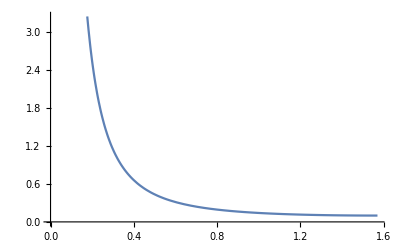

```mathematica
Plot[0.1/(1-Cos[x]^2),{x,0,π/2}]
```

```mathematica
f[x_]:=1-Cos[x/180*π]^2
```

```mathematica
f[30]//N
```

0.25

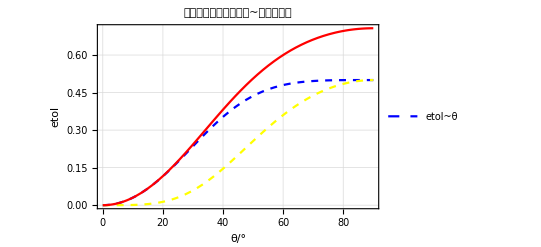

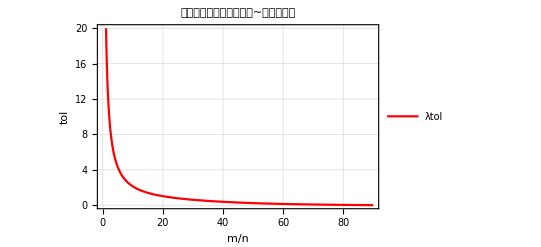

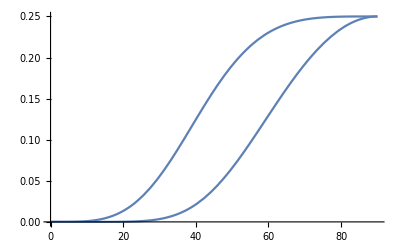

```mathematica
l=8/3;
g[θ_,λ_,p_]:=(Tan[θ/180*π]*p*λ-1)^2+(p λ Tan[θ/180*π] Sin[θ/180*π]^2)^2
Plot[{Sqrt@((p l Tan[t/180*π] Sin[t/180*π]^2)^2)/.(Minimize[g[t,l,p],p]//N)[[2]],Sqrt@((Tan[t/180*π]*p*l-1)^2)/.(Minimize[g[t,l,p],p]//N)[[2]],Sqrt@First@(Minimize[g[t,l,p],p]//N)},{t,0,90},PlotTheme->"Detailed",PlotLegends->{"etol~θ"},FrameLabel->{"θ/°","etol"},PlotLabel->"周期模型旋转前后容差~转角的关系",PlotStyle->{{Blue,Dashed},{Yellow,Dashed},Red}]
Plot[p/.(Minimize[g[t,8/3,p],p]//N)[[2]],{t,0,90},PlotTheme->"Detailed",PlotLegends->{"λtol","Δϕtol","etol"},FrameLabel->{"θ/°","m/n"},PlotLabel->"周期模型旋转前后晶格比~转角的关系",PlotStyle->Red,PlotRange->{{0,90},{0,20}}]

Plot[{(Tan[t/180*π]*p*8/3-1)^2,(p 8/3 Tan[t/180*π] Sin[t/180*π]^2)^2}/.(Minimize[g[t,8/3,p],p]//N)[[2]],{t,0,90}]
```

```mathematica
π/Range@10/Degree//N
```

{180.,90.,60.,45.,36.,30.,25.7143,22.5,20.,18.}

```mathematica
40/180
```

2/9

```mathematica
g[p_]:=(Tan[θ]*p*λ-1)^2+(p λ Tan[θ] Sin[θ]^2)^2
Solve[g'[p]==0,p]
Tan[θ]*p*λ-1/.{p->Cot[θ]/(λ (1+Sin[θ]^4))}//Simplify
p λ Tan[θ] Sin[θ]^2/.{p->Cot[θ]/(λ (1+Sin[θ]^4))}//Simplify
√(g[p]/.{p->Cot[θ]/(λ (1+Sin[θ]^4))})//Simplify
```

{{p→Cot[θ]/(λ (1+Sin[θ]^4))}}

-1+1/(1+Sin[θ]^4)

Sin[θ]^2/(1+Sin[θ]^4)

√(Sin[θ]^4/(1+Sin[θ]^4))

```mathematica
Clear[t]
p=Cot[#]/(8/3*(1+Sin[#]^4))&
t={10,20,30,35}/180*π
p/@t//N
```

Cot[#1]/(8/3 (1+Sin[#1]^4))&

{π/18,π/9,π/6,(7 π)/36}

{2.1248,1.0164,0.611312,0.483251}

```mathematica
m={21,1,10,10};
Sin[t]*24*m/2//N
Cos[t]*24*m/2//N
```

{43.7593,4.10424,60.,68.8292}

{248.172,11.2763,103.923,98.2982}

```mathematica
Clear[p]
Solve[D[(Tan[θ]*p*λ-1)^2+(Cos[θ]Sin[θ]*p*λ-1)^2,p]==0,p]//Simplify
```

{{p→(4 (3+Cos[2 θ]) Cot[θ])/(λ (11+4 Cos[2 θ]+Cos[4 θ]))}}